#### Telescopic method with Chebyshev interpolation

```mathematica
chebyshev1[0,x_]=1;
chebyshev1[1,x_]=x;
chebyshev1[n_,x_]:=(2 x chebyshev1[n-1]-chebyshev1[n-2])
```

```mathematica
interpolation[pol_,n_,a_,b_]:=Module[{pol1=pol},pol1=pol-Coefficient[pol,x^n]*(b-a)^n/2^(2n-1)*chebyshev1[n,(2x+a+b)/(b-a)];pol1]
```

```mathematica
telescopM[fun_,a_,b_,n_]:=Module[{pol=Normal@Series[fun,{x,0,n}]},Do[pol=interpolation[pol,n,a,b],n];pol]
```

#### Test1

```mathematica
pol1=telescopM[Cos[x],1,6,9]//N//Expand
```

1.-0.5 x^2+0.0416667 x^4-0.00138889 x^6+0.0000248016 x^8

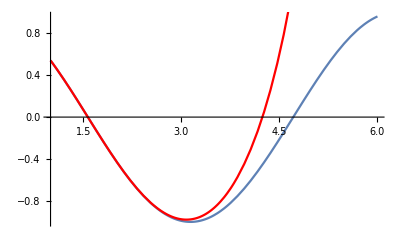

```mathematica
Show[{Plot[Cos[k],{k,1,6}],Plot[pol1/.x->k,{k,1,6},PlotStyle->Red]}]
```

#### Test2

```mathematica
pol2=telescopM[Cos[x],1,6,15]//N//Expand
```

1.-0.5 x^2+0.0416667 x^4-0.00138889 x^6+0.0000248016 x^8-2.75573×10^-7 x^10+2.08768×10^-9 x^12-1.14707×10^-11 x^14

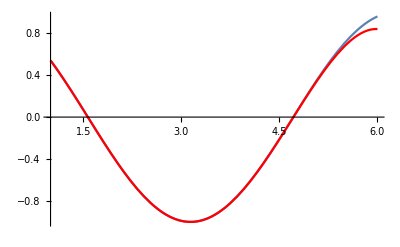

```mathematica
Show[{Plot[Cos[k],{k,1,6}],Plot[pol2/.x->k,{k,1,6},PlotStyle->Red]}]
```